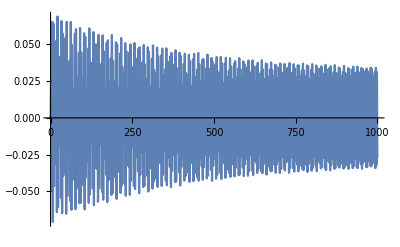

```mathematica
res=NDSolve[{y''[t]==-0.005y'[t]-2.4Cos[y[t]]Sin[y[t]]+0.05Sin[2t],y[0]==0.0001,y'[0]==0},y,{t,0,1000}];
Plot[y[t]/.res,{t,0,1000},ImageSize->Full]
```

```mathematica
pics=Table[Graphics[Rotate[Rectangle[{-2,0},{2,0.3}],First[(y[t]/.res)]],ImagePadding->150,ImageSize->Large],{t,0,15,0.033}];
ListAnimate[pics]
```

```mathematica
Export["test.mov",pics]
```

test.mov

```mathematica
Anim
```